{r0→(√(ck (y-y^(5-k)))-ck y Tan[thv])/ck}

{r→-y Cos[phi] Tan[thv]+√(r0^2+2 r0 y Tan[thv]+y^2 Cos[phi]^2 Tan[thv]^2)}

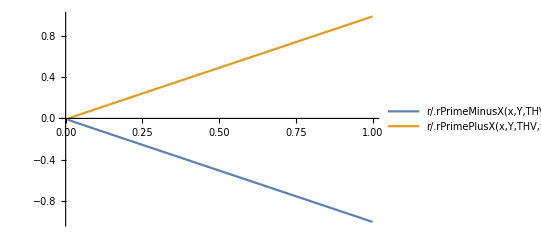

{r→-y Cos[phi] Tan[thv]+√(-y^2 Sin[phi]^2 Tan[thv]^2)}

{r→-y Cos[phi] Tan[thv]+√(1-y^2 Sin[phi]^2 Tan[thv]^2)}

Part::partw: Part 2 of {r0→0.00617954} does not exist.

ReplaceAll::reps: {{r0→0.00617954}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {r0→0.195409} does not exist.

ReplaceAll::reps: {{r0→0.195409}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {r0→0.276281} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{r0→0.276281}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of {r0→0.00617954} does not exist.

ReplaceAll::reps: {{r0→0.00617954}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {r0→0.195409} does not exist.

ReplaceAll::reps: {{r0→0.195409}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {r0→0.276281} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{r0→0.276281}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(*Clear["Global`*"]*)

(*Function definitions*)
ck[k_]:=(4-k)*(5-k)^((-(5-k))/(4-k));
xsq[r_,y_,thv_,phi_,k_]:=y^2*Tan[thv]^2+2*r*y*Tan[thv]*Cos[phi]+r^2;
chi[x_,y_,k_]:=(y-ck[k]*x)/y^(5-k);

(*Constant definitions*)
TORAD=π/180.;
Y=0.1;
R0=0.1;
THV=6.0*TORAD;
PHI=45.0*TORAD;
K=0.0;

(*Solve for y+/-(x)*)
yRoots[y_,x_,k_]:=y-y^(5-k)-ck[k]*x^2;
Manipulate[Plot[yRoots[y,x,0.0],{y,0,1}],{x,0,1}];
NSolve[yRoots[y,0.5,0.0]==0,y];

(*Solve for r0'_max(y|C)*)
r0MaxVals=Solve[y-y^(5-k)==ck*(y^2*Tan[thv]^2+2*r0*y*Tan[thv]+r0^2),r0];
r0Max[yVal_,tVal_,kVal_,ckVal_]:=r0MaxVals[[2]]/.{y->yVal,thv->tVal,k->kVal,ck->ckVal};
r0Max[y,thv,k,ck]//FullSimplify
Manipulate[Plot[r0/.r0Max[y,thv*TORAD,0.0,ck[0.0]][[2]],{y,0.000000001,1},PlotLegends->"Expressions"],{thv,0,15,3}]

(*Solve for r'*)
rPrimeVals=Solve[r^2+2*r*y*Tan[thv]*Cos[phi]==r0^2+2*y*r0*Tan[thv],r]//Simplify;
rPrimePlus[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[1]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
rPrimeMinus[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[2]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
rPrime[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[2]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
PhiIntegrand[rVal_,yVal_,tVal_,pVal_,kVal_]:=(r/rVal)^2/.rPrime[rVal,yVal,tVal,pVal,kVal];
PhiInt[rVal_,yVal_,tVal_,kVal_]:=NIntegrate[PhiIntegrand[rVal,yVal,tVal,phi,kVal],{phi,0,2*π}];
Plot[{r/.rPrimeMinus[R0,Y,THV,phi,K],r/.rPrimePlus[R0,Y,THV,phi,K]},{phi,0,2*π},PlotLegends->"Expressions"];
rPrimeMinus[r0,y,thv,phi,k]
Manipulate[Plot[(r/r0)^2/.rPrimeMinus[r0,y,thv*TORAD,phi*TORAD,0.0],{phi,0,360}],{r0,0,1},{y,0,1},{thv,0,15,3}]

(*Solve for r'(x)*)
rPrimeValsX=Solve[xsq[r,y,thv,phi,k]==x^2,r];
rPrimeMinusX[xVal_,yVal_,tVal_,pVal_]:=rPrimeValsX[[1]]/.{x->xVal,y->yVal,thv->tVal,phi->pVal};
rPrimePlusX[xVal_,yVal_,tVal_,pVal_]:=rPrimeValsX[[2]]/.{x->xVal,y->yVal,thv->tVal,phi->pVal};
Plot[{r/.rPrimeMinusX[x,Y,THV,PHI],r/.rPrimePlusX[x,Y,THV,PHI]},{x,0,1},PlotLegends->"Expressions"]
rPrimePlusX[0,y,thv,phi]//FullSimplify
rPrimePlusX[1,y,thv,phi]//FullSimplify
Manipulate[Plot[{Tooltip[r/.rPrimePlusX[0,y,thv*TORAD,phi*TORAD],r/.rPrimePlusX[0,yy,thv*TORAD,phi*TORAD]],Tooltip[r/.rPrimePlusX[1,y,thv*TORAD,phi*TORAD],r/.rPrimePlusX[1,y,thv*TORAD,phi*TORAD]]},{y,0,1},PlotRange->{{0,1},{-1,1}},ImageSize->Large,PlotLegends->{r/.rPrimePlusX[0,y,thv*TORAD,phi*TORAD],r/.rPrimePlusX[1,y,thv*TORAD,phi*TORAD]}],{phi,0.0,360.0,15.0},{thv,0.0,15.0,3.0}];

(*Solve for r'(χ)*)
rPrimeValsChi=Solve[chi==(y-ck[k]*(y^2*Tan[thv]^2+2*r*y*Tan[thv]*Cos[phi]+r^2))/y^(5-k),r];
rPrimeMinusChi[chiVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeValsChi[[1]]/.{chi->chiVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
rPrimePlusChi[chiVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeValsChi[[2]]/.{chi->chiVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
Plot[{r/.rPrimeMinusChi[chi,Y,THV,PHI,K],r/.rPrimePlusChi[chi,Y,THV,PHI,K]},{chi,1,10000},PlotLegends->"Expressions"];
Manipulate[Plot[r/.rPrimePlusChi[chi,y+0.00000000001,thv,PHI,K],{chi,1,1000}],{thv,0.0,15.0*TORAD,0.01*TORAD},{y,0,1,0.1}];
rPrimePlusChi[1.0,y,thv,phi,k]//FullSimplify;

(*Plotting*)
Manipulate[Plot[PhiInt[r0,y,thv*TORAD,0.0],{r0,0.0,1.0}],{y,0.0,1.0,0.1},{thv,0.0,10.0,1.0}];
Manipulate[Plot[PhiIntegrand[R0,Y,THV,phi,K],{phi,0,2*π}],{THV,0.0,15.0*TORAD,0.01*TORAD}];
Manipulate[Plot[PhiInt[r0,Y,thv,K],{r0,0.0,0.5}],{thv,0.0,15.0*TORAD,0.01*TORAD}];
```